```mathematica
f[ρ_,ρ0_,μ_,σ_,α_]:=α(ⅇ^(-(-μ+α Log[ρ/ρ0])^2/(2 σ^2)))/(√(2 π) ρ σ);
```

```mathematica
Integrate[f[ρ,ρ0,μ,σ,α],{ρ,0,Infinity},Assumptions->{σ>0,α>0,ρ0>0,μ>0}]
Integrate[ρ f[ρ,ρ0,μ,σ,α],{ρ,0,Infinity},Assumptions->{σ>0,α>0}]
Integrate[(ρ-ⅇ^((2 α μ+σ^2)/(2 α^2)) ρ0)^2 f[ρ,ρ0,μ,σ,α],{ρ,0,Infinity},Assumptions->{σ>0,α>0}]
Integrate[Log[ρ/ρ0]f[ρ,ρ0,μ,σ,α],{ρ,0,Infinity},Assumptions->{σ>0,α>0,ρ0>0,μ>0}]
```

1

ⅇ^((2 α μ+σ^2)/(2 α^2)) ρ0

ⅇ^((2 α μ+σ^2)/α^2) (-1+ⅇ^(σ^2/α^2)) ρ0^2

μ/α

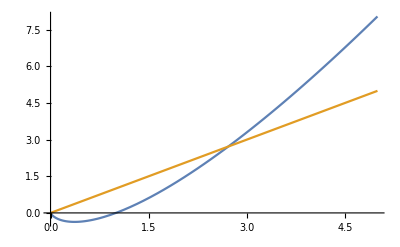

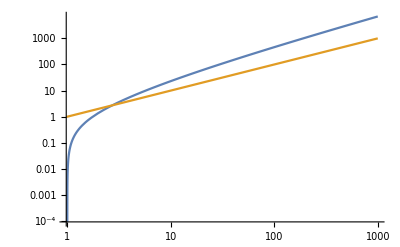

```mathematica
Plot[{x Log[x],x},{x,0,5}]
LogLogPlot[{x Log[x],x},{x,0,10^3}]
```

```mathematica
Solve[y==c x Log[x/x0],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→y/(c ProductLog[y/(c x0)])}}

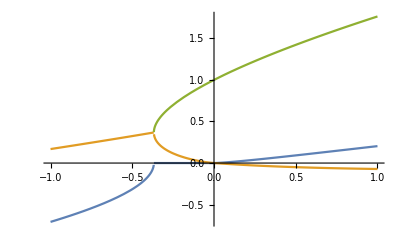

```mathematica
Plot[{Im@(y/ProductLog[-1,y]),Re@(y/ProductLog[-1,y]),y/ProductLog[0,y]},{y,-1,1}]
```

```mathematica
D[c x Log[x/x0],x]
```

c+c Log[x/x0]

```mathematica
Solve[c+c Log[x/x0]==0,x]
```

{{x→x0/ⅇ}}

```mathematica
c x Log[x/x0]/.x->x0/ⅇ
```

-(c x0)/ⅇ

```mathematica
g[ϵ_,μ_,σ_,α_,c_,ρ0_,ρ1_]:=1/(√(2π σ^2))(α/ϵ ProductLog[0,ϵ/(c ρ1)]/(1+Log[(ϵ/(c ρ1))/ProductLog[0,ϵ/(c ρ1)]])Exp[-(α Log[(ϵ/(c ρ0))/ProductLog[0,ϵ/(c ρ1)]]-μ)^2/(2 σ^2)]-α/ϵ ProductLog[-1,ϵ/(c ρ1)]/(1+Log[(ϵ/(c ρ1))/ProductLog[-1,ϵ/(c ρ1)]])Exp[-(α Log[(ϵ/(c ρ0))/ProductLog[-1,ϵ/(c ρ1)]]-μ)^2/(2 σ^2)]HeavisideTheta[-ϵ])HeavisideTheta[ϵ+c ρ1/E];
```

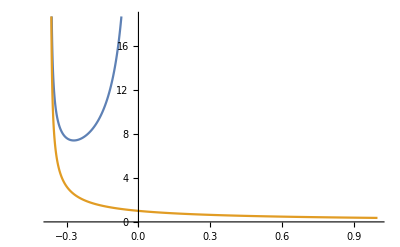

```mathematica
With[{μ=1,σ=0.5,α=1,c=1,ρ0=1,ρ1=1},Plot[{-α/ϵ ProductLog[-1,ϵ/(c ρ1)]/(1+Log[(ϵ/(c ρ1))/ProductLog[-1,ϵ/(c ρ1)]]),α/ϵ ProductLog[0,ϵ/(c ρ1)]/(1+Log[(ϵ/(c ρ1))/ProductLog[0,ϵ/(c ρ1)]])},{ϵ,-c ρ1/E,1},PlotPoints->{1000}]]
```

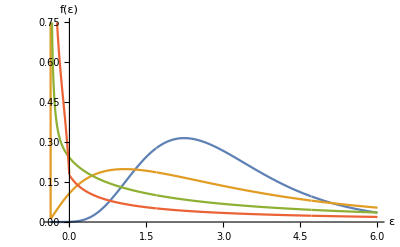

```mathematica
With[{μ=1,α=1,c=1,ρ0=1,ρ1=1},Plot[{g[x,μ,0.25,α,c,ρ0,ρ1],g[x,μ,0.5,α,c,ρ0,ρ1],g[x,μ,1,α,c,ρ0,ρ1],g[x,μ,2,α,c,ρ0,ρ1]},{x,-c ρ1/E,6},PlotRange->{0,0.75},AxesLabel->{"ε","f(ε)"}]]
```

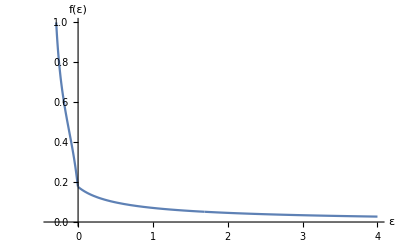

```mathematica
With[{μ=1,α=1,c=1,ρ0=1,ρ1=1},Plot[g[x,μ,2,α,c,ρ0,ρ1],{x,-c ρ1/E,4},PlotRange->{0,1},AxesLabel->{"ε","f(ε)"}]]
```

```mathematica
With[{μ=1,α=1,c=1,ρ0=1,ρ1=1},NIntegrate[g[x,μ,2,α,c,ρ0,ρ1],{x,-c ρ1/E,10^5}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.0225565}. NIntegrate obtained 0.99975 and 0.00121976 for the integral and error estimates.

0.99975

```mathematica
Solve[α Log[(ϵ/(c ρ0))/ProductLog[0,ϵ/(c ρ1)]]==x,ϵ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϵ→(c ⅇ^(x/α) ρ0 (x+α Log[ρ0/ρ1]))/α}}

```mathematica
D[α Log[(ϵ/(c ρ0))/ProductLog[-1,ϵ/(c ρ1)]],ϵ]//Simplify
```

(α ProductLog[-1,ϵ/(c ρ1)])/(ϵ+ϵ ProductLog[-1,ϵ/(c ρ1)])

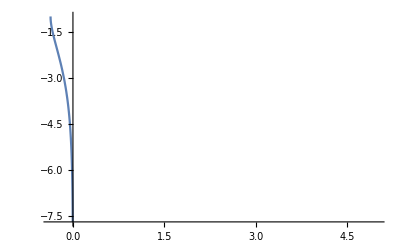

```mathematica
With[{α=1,c=1,ρ0=1,ρ1=1},Plot[α Log[(ϵ/(c ρ0))/ProductLog[-1,ϵ/(c ρ1)]],{ϵ,-c ρ1/E,5}]]
```

```mathematica
Limit[α Log[(ϵ/(c ρ0))/ProductLog[-1,ϵ/(c ρ1)]],ϵ->-c ρ1/E]
```

lim_(ϵ→-(c ρ1)/ⅇ) α Log[ϵ/(c ρ0 ProductLog[-1,ϵ/(c ρ1)])]

```mathematica
ProductLog[-1,-1/ⅇ]//N
```

-1.

```mathematica
α Log[(ϵ/(c ρ0))/ProductLog[0,ϵ/(c ρ1)]]/.ϵ->-c ρ1/E
```

α Log[ρ1/(ⅇ ρ0)]

```mathematica
Integrate[1/(√(2π σ^2))(c ρ0)/α E^(x/α)(x+α Log[ρ0/ρ1])E^(-(x-μ)^2/(2 σ^2)),{x,-Infinity,Infinity},Assumptions->{σ>0}]//Distribute
```

(c ⅇ^((2 α μ+σ^2)/(2 α^2)) μ ρ0)/α+(c ⅇ^((2 α μ+σ^2)/(2 α^2)) ρ0 σ^2)/α^2+c ⅇ^((2 α μ+σ^2)/(2 α^2)) ρ0 Log[ρ0/ρ1]

```mathematica
(c ρ0)/α(μ+σ^2/α+α Log[ρ0/ρ1]) ⅇ^((2 α μ+σ^2)/(2 α^2))
```

```mathematica
Integrate[1/(√(2π σ^2))((c ρ0)/α E^(x/α)(x+α Log[ρ0/ρ1])-((c ⅇ^((2 α μ+σ^2)/(2 α^2)) μ ρ0)/α+(c ⅇ^((2 α μ+σ^2)/(2 α^2)) ρ0 σ^2)/α^2+c ⅇ^((2 α μ+σ^2)/(2 α^2)) ρ0 Log[ρ0/ρ1]))^2 E^(-(x-μ)^2/(2 σ^2)),{x,-Infinity,Infinity},Assumptions->{σ>0}]//Distribute
```

-(c^2 ⅇ^((2 α μ+σ^2)/α^2) ρ0^2 (α μ+σ^2+α^2 Log[ρ0/ρ1])^2)/α^4+(c^2 ⅇ^(σ^2/α^2+(2 α μ+σ^2)/α^2) ρ0^2 (α^2 μ^2+α (α+4 μ) σ^2+4 σ^4+α^2 Log[ρ0/ρ1] (2 α μ+4 σ^2+α^2 Log[ρ0/ρ1])))/α^4

```mathematica
-(c^2 ⅇ^((2 α μ+σ^2)/α^2) ρ0^2 (α μ+σ^2+α^2 Log[ρ0/ρ1])^2)/α^4+(c^2 ⅇ^(σ^2/α^2+(2 α μ+σ^2)/α^2) ρ0^2 (α^2 μ^2+α (α+4 μ) σ^2+4 σ^4+α^2 Log[ρ0/ρ1] (2 α μ+4 σ^2+α^2 Log[ρ0/ρ1])))/α^4//FullSimplify
```

1/α^4 c^2 ⅇ^((2 α μ+σ^2)/α^2) ρ0^2 (-(α μ+σ^2+α^2 Log[ρ0/ρ1])^2+ⅇ^(σ^2/α^2) (α^2 μ^2+α (α+4 μ) σ^2+4 σ^4+α^2 Log[ρ0/ρ1] (2 α μ+4 σ^2+α^2 Log[ρ0/ρ1])))

```mathematica
Solve[{μ2==ρ0 Exp[(2α μ+σ^2)/(2 α^2)],σ2==ρ0 √(E^((σ/α)^2)-1)Exp[(2α μ+σ^2)/(2 α^2)]},{μ,σ}]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is Log[ⅇ^((2 α μ+σ^2)/α^2)]-2 Log[μ2/ρ0] == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{μ→1/2 α (-Log[1+ⅇ^(-2 (Log[μ2/ρ0]+Log[ρ0]-Log[σ2]))]+2 Log[μ2/ρ0]),σ→-α √Log[1+ⅇ^(-2 (Log[μ2/ρ0]+Log[ρ0]-Log[σ2]))]},{μ→1/2 α (-Log[1+ⅇ^(-2 (Log[μ2/ρ0]+Log[ρ0]-Log[σ2]))]+2 Log[μ2/ρ0]),σ→α √Log[1+ⅇ^(-2 (Log[μ2/ρ0]+Log[ρ0]-Log[σ2]))]}}

```mathematica
Simplify[(c ρ0)/α(μ+σ^2/α+α Log[ρ0/ρ1]) ⅇ^((2 α μ+σ^2)/(2 α^2))/.{σ->α √Log[σρ^2/μρ^2+1],μ->α Log[(μρ^2/ρ0)/(√(σρ^2+μρ^2))]},Assumptions->{ρ0>0,ρ1>0,μρ>0,σρ>0}]
```

c μρ Log[(√(μρ^2+σρ^2))/ρ1]

```mathematica
FullSimplify[1/α^4 c^2 ⅇ^((2 α μ+σ^2)/α^2) ρ0^2 (-(α μ+σ^2+α^2 Log[ρ0/ρ1])^2+ⅇ^(σ^2/α^2) (α^2 μ^2+α (α+4 μ) σ^2+4 σ^4+α^2 Log[ρ0/ρ1] (2 α μ+4 σ^2+α^2 Log[ρ0/ρ1])))/.{σ->α √Log[σρ^2/μρ^2+1],μ->α Log[(μρ^2/ρ0)/(√(σρ^2+μρ^2))]},Assumptions->{ρ0>0,ρ1>0,μρ>0,σρ>0,α>0}]
```

1/4 c^2 (σρ^2 (-4 Log[μρ]+2 Log[ρ1]+Log[μρ^2+σρ^2])^2+4 (μρ^2+σρ^2+(μρ^2+2 σρ^2) (4 Log[μρ]-2 Log[ρ1]-Log[μρ^2+σρ^2])) Log[1+σρ^2/μρ^2]+4 (3 μρ^2+4 σρ^2) Log[1+σρ^2/μρ^2]^2)